# Numerical Methods Practicals

## Practical 1: Bisection Method

```mathematica
bisection[f_, ao_ ,bo_ , n_ ] := Module[{},a=N[ao];
b=N[bo];
If[f[a]*f[b]>0, Print["Bisection Method can not applied"];
Return[]];
p = (a+b)/2;
i=1;
While[i≤n,
If[f[a]*f[p]<0, b=p , a=p];
Print[i, "        ", a , "        " , b];
i++;
p=(a+b)/2];
Print["Root=" ,p]];
```

Q1. Perform five iterations of the bisection method to obtain the smallest positive root of the equation, f(x) = x^3 - 5x + 1 = 0 .

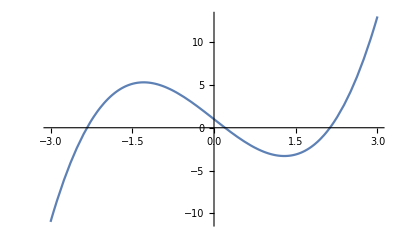

1        0.        0.5

2        0.        0.25

3        0.125        0.25

4        0.1875        0.25

5        0.1875        0.21875

Root=0.203125

```mathematica
f[x_] :=x^3 -5x+1;
Plot[f[x] , {x , -3 , 3}]
bisection[f , 0 , 1 , 5];
```

Q2. Perform five iterations of the bisection method to obtain the smallest positive root of the equation, f(x) = x^2 - 5 = 0.

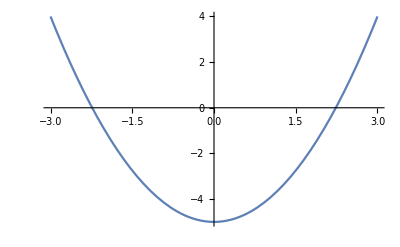

1        2.        3.

2        2.        3.

3        2.        3.

4        2.        3.

5        2.        3.

Root=2.5

```mathematica
f[x_] :=x^2 - 5;
Plot[f[x] , {x , -3, 3}]
bisection[f[x] , 2 , 3 , 5];
```

Q3. Perform five iterations of the bisection method to obtain the smallest positive root of the equation, f(x) =  x^3 - 2x - 5 = 0.

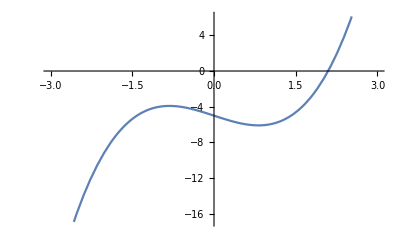

1        2.        2.5

2        2.        2.25

3        2.        2.125

4        2.0625        2.125

5        2.09375        2.125

Root=2.10938

```mathematica
f[x_] :=x^3-2x-5;
Plot[f[x] , {x , -3 , 3}]
bisection[f , 2 , 3 , 5];
```

Q4. Perform five iterations of the bisection method to obtain the smallest positive root of the equation, f(x) =  x^4 - x - 10 = 0.

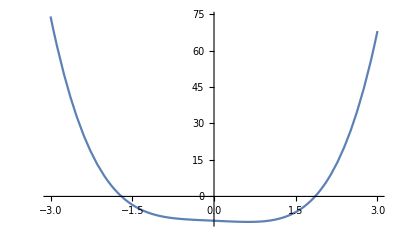

1        1.5        2.

2        1.75        2.

3        1.75        1.875

4        1.8125        1.875

5        1.84375        1.875

Root=1.85938

```mathematica
f[x_]:= x^4 -x -10;
Plot[f[x], {x , -3 , 3}]
bisection[f , 1 , 2 , 5]
```

## Practical 2(a): Secant Method

```mathematica
secant[f_, ao_ ,bo_ , n_ ]:= Module[{},p0=N[ao];
p1=N[bo];
If[f[p0]*f[p1]>0, Print["Secant Method can not applied"];
Return[]];
i=1;
While[i≤n,
p2 = N[p1-((p1-p0)*f[p1]/(f[p1]-f[p0]))];
Print[i, "        ", p0 , "        " , p1];
i++;
p0=p1;
p1=p2];
Print[" Root=" ,p2]];
```

Q1. Perform five iterations of the secant method to obtain the smallest positive root of the equation, f(x) =  x^3 +x^2-3x-3.

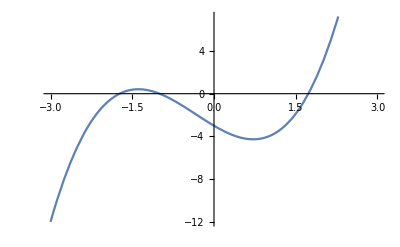

1        1.        2.

2        2.        1.57143

3        1.57143        1.70541

4        1.70541        1.73514

5        1.73514        1.732

Root=1.73205

```mathematica
f[x_] :=x^3 +x^2-3x-3;
Plot[f[x] ,{x ,  -3 , 3}]
secant[f , 1 , 2 , 5];
```

Q2. Perform five iterations of the secant method to obtain the smallest positive root of the equation, f(x) = x^3 - 5x + 1 = 0 .

```mathematica
f[x_] :=x^3-5x+1;
Plot[f[x] ,{x ,  -3 , 3}]
secant[f , 0 , 1 , 5];
```

-Graphics-

1        0.        1.

2        1.        0.25

3        0.25        0.186441

4        0.186441        0.201736

5        0.201736        0.20164

Root=0.20164

Q3. Perform five iterations of the secant method to obtain the smallest positive root of the equation, f(x) =  x^3 - 2x - 5 = 0.

```mathematica
f[x_] :=x^3-2x-5;
Plot[f[x] ,{x ,  -3 , 3}]
secant[f , 2 , 3 , 5];
```

-Graphics-

1        2.        3.

2        3.        2.05882

3        2.05882        2.08126

4        2.08126        2.09482

5        2.09482        2.09455

Root=2.09455

Q4. Perform five iterations of the secant method to obtain the smallest positive root of the equation, f(x) =  x^4 - x - 10 = 0.

```mathematica
f[x_] :=x^4-x-10;
Plot[f[x] ,{x ,  -3 , 3}]
secant[f , 1 , 2 , 5];
```

-Graphics-

1        1.        2.

2        2.        1.71429

3        1.71429        1.83853

4        1.83853        1.85778

5        1.85778        1.85555

Root=1.85558

## Practical 2(b): Regula-Falsi Method

```mathematica
RegulaFalsi[f_, ao_ ,bo_ , n_ ]:= Module[{},p0=N[ao];
p1=N[bo];
If[f[p0]*f[p1]>0, Print["Secant Method cannot applied"];
Return[]];
i=1;
While[i≤n,
p2 = N[p1-((p1-p0)*f[p1]/(f[p1]-f[p0]))];
Print[i, "        ", p0 , "        " , p1];
i++;
p0=p1;
p1=p2];
Print[" Root=" ,p2]];
```

Q1.  Find the smallest positive root of f(x) = x^3 + 4x^2 - 10.

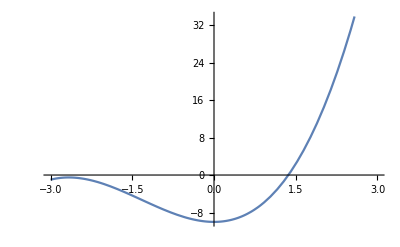

1        1.        2.

2        2.        1.26316

3        1.26316        1.33883

4        1.33883        1.36662

5        1.36662        1.36521

6        1.36521        1.36523

Root=1.36523

```mathematica
f[x_]=x^3+4x^2-10;
Plot[f[x], {x, -3, 3}]
RegulaFalsi[f, 1, 2, 6]
```

Q2.  Find the smallest positive root of f(x) = 5x^4 + 2x^3 +x - 10.

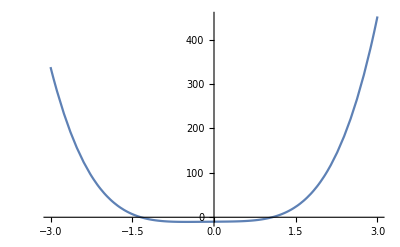

1        1.        2.

2        2.        1.02222

3        1.02222        1.03734

4        1.03734        1.06954

5        1.06954        1.06763

Root=1.06771

```mathematica
f[x_]=5x^4+2x^3+x-10;
Plot[f[x], {x, -3, 3}]
RegulaFalsi[f, 1, 2, 5]
```

Q3.  Find the smallest positive root of f(x) = x^4 - x - 10 .

```mathematica
f[x_]=x^4-x-10;
Plot[f[x], {x, -3, 3}]
RegulaFalsi[f, 1, 2, 5]
```

-Graphics-

1        1.        2.

2        2.        1.71429

3        1.71429        1.83853

4        1.83853        1.85778

5        1.85778        1.85555

Root=1.85558

Q4.  Find the smallest positive root of f(x) = x^3 - 2x - 5  .

```mathematica
f[x_]=x^3-2x-5;
Plot[f[x], {x, -3, 3}]
RegulaFalsi[f, 2, 3, 5]
```

-Graphics-

1        2.        3.

2        3.        2.05882

3        2.05882        2.08126

4        2.08126        2.09482

5        2.09482        2.09455

Root=2.09455

## Practical 3: Newton-Raphson Method

```mathematica
newtonraphson[f_ , p0_ , n_ ]:= Module[{}, pold = N[p0];
i=1;
pnew=0;
df[x_]=D[f[x], x];
While[i<= n ,
pnew = N[pold-N[f[pold]]/N[df[pold]]];
Print[i, "       ", pnew];
i++;
pold=pnew];
Print[" Root =", pnew]]
```

Q1. Find the smallest positive root of x-2sin(x), near x=1.9 correct to three decimal places using Newton-Raphson method.

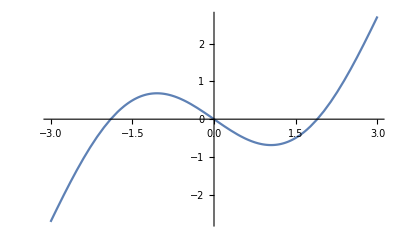

1       1.89551

2       1.89549

3       1.89549

4       1.89549

5       1.89549

Root =1.89549

```mathematica
f[x_]:=x-2Sin[x];
Plot[f[x], {x, -3 , 3}]
newtonraphson[f, 1.9 , 5]
```

Q2. Find the smallest positive root of x^4-x-10, correct to three decimal places using Newton-Raphson method.

```mathematica
f[x_]:=x^4-x-10;
Plot[f[x], {x, -3 , 3}]
newtonraphson[f, 1.5 , 5]
```

-Graphics-

1       2.015

2       1.87409

3       1.85587

4       1.85558

5       1.85558

Root =1.85558

Q3. Find the smallest positive root of x^3-6x+4, correct to three decimal places using Newton-Raphson method.

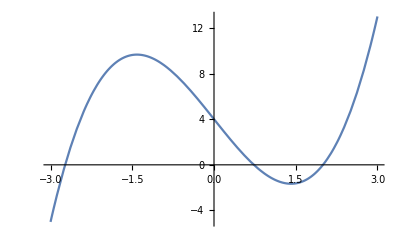

1       3.66667

2       2.75512

3       2.25533

4       2.04584

5       2.00195

Root =2.00195

```mathematica
f[x_]:=x^3-6x+4;
Plot[f[x], {x, -3 , 3}]
newtonraphson[f, 1.5 , 5]
```

Q4. Find the smallest positive root of 3x-cos(x)-1=0, using Newton-Raphson method.

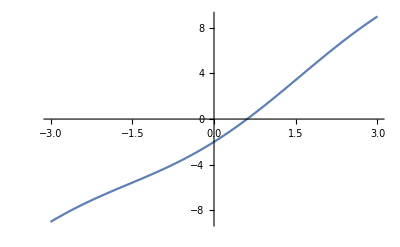

1       0.608519

2       0.607102

3       0.607102

4       0.607102

5       0.607102

Root =0.607102

```mathematica
f[x_]:=3x-Cos[x]-1;
Plot[f[x], {x, -3 , 3}]
newtonraphson[f, 0.5 , 5]
```

## Practical 4(a) : Gaussian Elimination Method

Q1.  Solve the system of linear equation.

```mathematica
m = ({{1, 1, 1}, {1, 1, -1}, {1, -1, -1}});
x = ({{x1}, {x2}, {x3}});
b = ({{1}, {2}, {-1}});
m.x==b
```

{{x1+x2+x3},{x1+x2-x3},{x1-x2-x3}}=={{1},{2},{-1}}

```mathematica
ArrayFlatten[{{m , b}}]//MatrixForm
```

(1 | 1 | 1 | 1
1 | 1 | -1 | 2
1 | -1 | -1 | -1)

```mathematica
Flatten[LinearSolve[m, b]]
```

{0,3/2,-1/2}

```mathematica
ClearAll
```

ClearAll

Q2. Solve the system of linear equation.

```mathematica
m = ({{2, 5, 2}, {3, -2, 4}, {-6, 1, -7}});
x = ({{x1}, {x2}, {x3}});
b = ({{-38}, {17}, {-12}});
m.x==b
```

{{2 x1+5 x2+2 x3},{3 x1-2 x2+4 x3},{-6 x1+x2-7 x3}}=={{-38},{17},{-12}}

```mathematica
ArrayFlatten[{{m , b}}]//MatrixForm
```

(2 | 5 | 2 | -38
3 | -2 | 4 | 17
-6 | 1 | -7 | -12)

```mathematica
Flatten[LinearSolve[m, b]]
```

{3,-8,-2}

```mathematica
ClearAll
```

ClearAll

Q3. Solve the system of linear equations.

```mathematica
m = ({{3, 0, -9}, {7, -4, -1}, {4, 6, 5}});
x = ({{x1}, {x2}, {x3}});
b = ({{33}, {-15}, {-6}});
m.x==b
```

{{3 x1-9 x3},{7 x1-4 x2-x3},{4 x1+6 x2+5 x3}}=={{33},{-15},{-6}}

```mathematica
ArrayFlatten[{{m , b}}]//MatrixForm
```

(3 | 0 | -9 | 33
7 | -4 | -1 | -15
4 | 6 | 5 | -6)

```mathematica
Flatten[LinearSolve[m, b]]
```

{-1,3,-4}

```mathematica
ClearAll
```

ClearAll

Q4. Solve the system of linear equations.

```mathematica
m = ({{4, -1, 3}, {0, 2, 5}, {-6, 1, -3}});
x = ({{x1}, {x2}, {x3}});
b = ({{5}, {9}, {10}});
m.x==b
```

{{4 x1-x2+3 x3},{2 x2+5 x3},{-6 x1+x2-3 x3}}=={{5},{9},{10}}

```mathematica
ArrayFlatten[{{m , b}}]//MatrixForm
```

(4 | -1 | 3 | 5
0 | 2 | 5 | 9
-6 | 1 | -3 | 10)

```mathematica
Flatten[LinearSolve[m, b]]
```

{-15/2,-148/11,79/11}

```mathematica
ClearAll
```

ClearAll

## Practical 4(b): Gauss-Jordan Method

Q1. Solve the system of linear equation.

```mathematica
m={{1,1,1},{1,1,-1},{1,-1,-1}};
x={{x1},{y1},{z1}};
b={1,2,-1};
MatrixForm[a=Transpose[Join[Transpose[m],{b}]]]
```

(1 | 1 | 1 | 1
1 | 1 | -1 | 2
1 | -1 | -1 | -1)

```mathematica
r=RowReduce[a]
```

{{1,0,0,0},{0,1,0,3/2},{0,0,1,-1/2}}

```mathematica
x=r[[All,-1]]
```

{0,3/2,-1/2}

Q2. Solve the system of linear equations.

```mathematica
m={{2,5,2},{3,-2,4},{-6,1,-7}};
x={{x1},{y1},{z1}};
b={-38,17,-12};
MatrixForm[a=Transpose[Join[Transpose[m],{b}]]]
```

(2 | 5 | 2 | -38
3 | -2 | 4 | 17
-6 | 1 | -7 | -12)

```mathematica
r=RowReduce[a]
```

{{1,0,0,3},{0,1,0,-8},{0,0,1,-2}}

```mathematica
x=r[[All,-1]]
```

{3,-8,-2}

Q3. Solve the system of linear equations.

```mathematica
m={{3,0,-9},{7,-4,-1},{4,6,5}};
x={{x1},{y1},{z1}};
b={33,-15,-6};
MatrixForm[a=Transpose[Join[Transpose[m],{b}]]]
```

(3 | 0 | -9 | 33
7 | -4 | -1 | -15
4 | 6 | 5 | -6)

```mathematica
r=RowReduce[a]
```

{{1,0,0,-1},{0,1,0,3},{0,0,1,-4}}

```mathematica
x=r[[All,-1]]
```

{-1,3,-4}

Q4. Solve the system of linear equations.

```mathematica
m={{4,-1,3},{0,2,5},{-6,1,-3}};
x={{x1},{y1},{z1}};
b={5,9,10};
MatrixForm[a=Transpose[Join[Transpose[m],{b}]]]
```

(4 | -1 | 3 | 5
0 | 2 | 5 | 9
-6 | 1 | -3 | 10)

```mathematica
r=RowReduce[a]
```

{{1,0,0,-15/2},{0,1,0,-148/11},{0,0,1,79/11}}

```mathematica
x=r[[All,-1]]
```

{-15/2,-148/11,79/11}

## Practical 5(a): Jacobi Method

```mathematica
Jacobi[ao_,bo_,po_,max_]:=Module[{A=N[ao],
B=N[bo],i,j,k=0,n=Length[po],p=po,pold=po},Print["Po=",p];
While[k<max,
For[i=1,i<=n,i++,
p[[i]]=(1/A[[i,i]])*(B[[i]]+A[[i,i]]*pold[[i]]-Sum[A[[i,j]]*pold[[j]],{j,1,n}])];
Print["P",k+1,"=",p];
pold=p;
k=k+1;];
Return[p];];
```

Q1. Solve the system of linear equations.

```mathematica
m={{1,1,1},{1,1,-1},{1,-1,-1}};
x={{x1},{y1},{z1}};
b={1,2,-1};
Print[MatrixForm[m],MatrixForm[x],"=",MatrixForm[b]];
```

(1 | 1 | 1
1 | 1 | -1
1 | -1 | -1)(x1
y1
z1)=(1
2
-1)

```mathematica
p={1,1,1};
X=Jacobi[m,b,p,5];
```

Po={1,1,1}

P1={-1.,2.,1.}

P2={-2.,4.,-2.}

P3={-1.,2.,-5.}

P4={4.,-2.,-2.}

P5={5.,-4.,7.}

Q2. Solve the system of linear equations.

```mathematica
m={{2,5,2},{3,-2,4},{-6,1,-7}};
x={{x1},{y1},{z1}};
b={-38,17,-12};
Print[MatrixForm[m],MatrixForm[x],"=",MatrixForm[b]];
```

(2 | 5 | 2
3 | -2 | 4
-6 | 1 | -7)(x1
y1
z1)=(-38
17
-12)

```mathematica
p={0,0,0};
X=Jacobi[m,b,p,5];
```

Po={0,0,0}

P1={-19.,-8.5,1.71429}

P2={0.535714,-33.5714,16.7857}

P3={48.1429,25.875,-3.54082}

P4={-80.1467,56.6327,-35.8546}

P5={-124.727,-200.429,78.5018}

Q3. Solve the system of linear equations.

```mathematica
m={{2,5},{1,2}};
x={{x1},{y1}};
b={21,8};
Print[MatrixForm[m],MatrixForm[x],"=",MatrixForm[b]];
```

(2 | 5
1 | 2)(x1
y1)=(21
8)

```mathematica
p={0,0};
X=Jacobi[m,b,p,3];
```

Po={0,0}

P1={10.5,4.}

P2={0.5,-1.25}

P3={13.625,3.75}

Q4. Solve the system of linear equations.

```mathematica
m={{3,0,-9},{7,-4,-1},{4,6,5}};
x={{x1},{y1},{z1}};
b={33,-15,-6};
Print[MatrixForm[m],MatrixForm[x],"=",MatrixForm[b]];
```

(3 | 0 | -9
7 | -4 | -1
4 | 6 | 5)(x1
y1
z1)=(33
-15
-6)

```mathematica
p={0,0, 0};
X=Jacobi[a,b,p,5];
```

Po={0,0,0}

P1={8.25,-7.5,2.}

P2={4.875,-12.5,-17.}

P3={17.875,35.,-11.9167}

P4={25.9375,22.2917,-22.0833}

P5={30.3854,47.7083,-42.4444}

## Practical 5(b): Gauss-Seidel Method

```mathematica
GaussSeidel[A0_,B0_,P0_,max_]:=Module[{A=N[A0],
B=N[B0],i,j,k=0,n=Length[P0],P=P0},Print[" P",0," = ",P];
While[k<max,
For[i=1,i<=n,i++,
P⟦i⟧=(1÷A⟦i,i⟧)*(B⟦i⟧+A⟦i,i⟧*P⟦i⟧-Sum[A⟦i,j⟧*P⟦j⟧,{j,1,n}])];
Print[" P",k+1," = ",P];
k=k+1;];
Return[P];];
```

Q1. Solve the system of linear equations.

```mathematica
m={{7,-2,1,2},{2,8,3,1},{-1,0,5,2},{0,2,-1,4}};
x={"x1","x2","x3","x4"};
b={3,-2,5,4};
Print[MatrixForm[m],MatrixForm[x]," = ",MatrixForm[b]]
```

(7 | -2 | 1 | 2
2 | 8 | 3 | 1
-1 | 0 | 5 | 2
0 | 2 | -1 | 4)(x1
x2
x3
x4) = (3
-2
5
4)

```mathematica
p={0,-1,1,1};
x=GaussSeidel[m,b,p,10];
```

P0 = {0,-1,1,1}

P1 = {-0.285714,-0.678571,0.542857,1.475}

P2 = {-0.264286,-0.571875,0.357143,1.37522}

P3 = {-0.178763,-0.511141,0.414158,1.35911}

P4 = {-0.164951,-0.53396,0.423366,1.37282}

P5 = {-0.176704,-0.536189,0.415531,1.37198}

P6 = {-0.17598,-0.533326,0.416013,1.37067}

P7 = {-0.174857,-0.533624,0.416762,1.371}

P8 = {-0.175145,-0.533875,0.41657,1.37108}

P9 = {-0.175211,-0.533796,0.416526,1.37103}

P10 = {-0.175168,-0.533784,0.416555,1.37103}

Q2. Solve the system of linear equations.

```mathematica
m={{45,2,3},{-3,22,2},{5,1,20}};
x={"x1","x2","x3"};
b={3,-2,5,4};
Print[MatrixForm[m],MatrixForm[x]," = ",MatrixForm[b]]
```

(45 | 2 | 3
-3 | 22 | 2
5 | 1 | 20)(x1
x2
x3) = (3
-2
5
4)

```mathematica
p={0,0, 0};
x=GaussSeidel[m,b,p,5];
```

P0 = {0,0,0}

P1 = {0.0666667,-0.0818182,0.237424}

P2 = {0.0544747,-0.105065,0.241635}

P3 = {0.0552272,-0.105345,0.24146}

P4 = {0.0552513,-0.105326,0.241453}

P5 = {0.0552509,-0.105325,0.241454}

Q3. Solve the system of linear equations.

```mathematica
m={{4,2,1},{1,5,-1},{1,1,8}};
x={"x1","x2","x3"};
b={14,10,20};
Print[MatrixForm[m],MatrixForm[x]," = ",MatrixForm[b]]
```

(4 | 2 | 1
1 | 5 | -1
1 | 1 | 8)(x1
x2
x3) = (14
10
20)

```mathematica
p={0,0, 0};
x=GaussSeidel[m,b,p,10];
```

P0 = {0,0,0}

P1 = {3.5,1.3,1.9}

P2 = {2.375,1.905,1.965}

P3 = {2.05625,1.98175,1.99525}

P4 = {2.01031,1.99699,1.99909}

P5 = {2.00173,1.99947,1.99985}

P6 = {2.0003,1.99991,1.99997}

P7 = {2.00005,1.99998,2.}

P8 = {2.00001,2.,2.}

P9 = {2.,2.,2.}

P10 = {2.,2.,2.}

Q4. Solve the system of linear equations.

```mathematica
m={{45,2,3},{-3,22,2},{5,1,20}};
x={{x1},{y1},{z1}};
b={58,47,67};
Print[MatrixForm[m],MatrixForm[x],"=",MatrixForm[b]];
```

(45 | 2 | 3
-3 | 22 | 2
5 | 1 | 20)(x1
y1
z1)=(58
47
67)

```mathematica
p={0,0, 0};
x=GaussSeidel[m,b,p,6];
```

P0 = {0,0,0}

P1 = {1.28889,2.31212,2.91217}

P2 = {0.991983,2.00689,3.00166}

P3 = {0.999583,1.99979,3.00011}

P4 = {1.,1.99999,3.}

P5 = {1.,2.,3.}

P6 = {1.,2.,3.}

## Practical 6(a): Lagrange’s Interpolation

Q1. Interpolate for the given data using Lagrange’s interpolation.

```mathematica
sum=0;
points={{-1,-2},{1,0},{4,63},{7,342}};
no=Length[points]
y=points⟦All,1⟧
f=points⟦All,2⟧
lagrange[no_,n_]:=Product[If[Equal[k,n],1,(x-y⟦k⟧)/(y⟦n⟧-y⟦k⟧)],{k,1,no}]
For[i=1,i≤no,i++,sum+=(f⟦i⟧*lagrange[no,i])]
Expand[sum]
sum/.x->5
```

4

{-1,1,4,7}

{-2,0,63,342}

-1+x^3

124

Q2. Interpolate for the given data using Lagrange’s interpolation.

```mathematica
sum=0;
points={{0,2},{1,3},{2,12},{5,147}};
no=Length[points]
y=points⟦All,1⟧
f=points⟦All,2⟧
lagrange[no_,n_]:=
Product[If[Equal[k,n],1,(x-y⟦k⟧)/(y⟦n⟧-y⟦k⟧)],{k,1,no}]
For[i=1,i≤no,i++,sum+=(f⟦i⟧*lagrange[no,i])]
Expand[sum]
sum/. x->2.5
```

4

{0,1,2,5}

{2,3,12,147}

2-x+x^2+x^3

21.375

Q3. Interpolate for the given data using Lagrange’s interpolation.

```mathematica
sum=0;
points= {{2, 2}, {3, 5}, {6, 10}};
no= Length[points]
y= points[[All, 1]]
f= points[[All, 2]]
lagrange[no_, n_]:=
Product[If[Equal[k , n], 1, (x-y[[k]])/y[[n]]-y[[k]]], {k, 1, no}]
For[i=1, i<=no, i++, sum+= (f[[i]]*lagrange[no, i])]
Expand[sum]
sum/.x->2.5
```

3

{2,3,6}

{2,5,10}

808/3-41 x+(4 x^2)/3

175.167

Q4. Interpolate for the given data using Lagrange’s interpolation.

```mathematica
sum=2;
points= {{1, 4}, {5, 7}, {8, 10}};
no= Length[points]
y= points[[All, 1]]
f= points[[All, 2]]
lagrange[no_, n_]:=
Product[If[Equal[k , n], 1, (x-y[[k]])/y[[n]]-y[[k]]], {k, 1, no}]
For[i=1, i<=no, i++, sum+= (f[[i]]*lagrange[no, i])]
Expand[sum]
sum/.x->4.5
```

3

{1,5,8}

{4,7,10}

628737/800-(51023 x)/400+(3549 x^2)/800

301.747

## Practical 6(b): Newton’s Interpolation

Q1. Interpolate for the given data using Newton’s interpolation.

```mathematica
sum=0;
points={{3,293},{5,508},{6,685},{9,764}};
n=Length[points]
y=points[[All,1]]
f=points[[All,2]]
dd[k_]:=
Sum[(f[[i]]/Product[If[Equal[j,i],1,(y[[i]]-y[[j]])],{j,1,k}]),{i,1,k}]
p[x_]=Sum[(dd[i]*Product[If[i<=j,1,x-y[[j]]],{j,1,i-1}]),{i,1,n}]
Simplify[p[x]]
Evaluate[p[2.5]]
```

4

{3,5,6,9}

{293,508,685,764}

293+215/2 (-3+x)+139/6 (-5+x) (-3+x)-365/36 (-6+x) (-5+x) (-3+x)

1/36 (44298-25797 x+5944 x^2-365 x^3)

312.566

Q2. Interpolate for the given data using Newton’s interpolation.

```mathematica
sum=1;
points={{1,103},{3,308},{6,485},{10,764}};
n=Length[points]
y=points[[All,1]]
f=points[[All,2]]
dd[k_]:=
Sum[(f[[i]]/Product[If[Equal[j,i],1,(y[[i]]-y[[j]])],{j,1,k}]),{i,1,k}]
p[x_]=Sum[(dd[i]*Product[If[i<=j,1,x-y[[j]]],{j,1,i-1}]),{i,1,n}]
Simplify[p[x]]
Evaluate[p[0.5]]
```

4

{1,3,6,10}

{103,308,485,764}

103+205/2 (-1+x)-87/10 (-3+x) (-1+x)+(1433 (-6+x) (-3+x) (-1+x))/1260

(-58050+211689 x-25292 x^2+1433 x^3)/1260

33.0561

Q3. Interpolate for the given data using Newton’s interpolation.

```mathematica
sum=1;
points={{10,113},{13,318},{16,585},{20,769}};
n=Length[points]
y=points[[All,1]]
f=points[[All,2]]
dd[k_]:=
Sum[(f[[i]]/Product[If[Equal[j,i],1,(y[[i]]-y[[j]])],{j,1,k}]),{i,1,k}]
p[x_]=Sum[(dd[i]*Product[If[i<=j,1,x-y[[j]]],{j,1,i-1}]),{i,1,n}]
Simplify[p[x]]
Evaluate[p[15.5]]
```

4

{10,13,16,20}

{113,318,585,769}

113+205/3 (-10+x)+31/9 (-13+x) (-10+x)-302/315 (-16+x) (-13+x) (-10+x)

1/315 (589555-153826 x+12863 x^2-302 x^3)

542.786

Q4. Interpolate for the given data using Newton’s interpolation.

```mathematica
sum=0;
points={{0,1},{1,14},{2,15},{4,5},{5,6}};
n=Length[points]
y=points[[All,1]]
f=points[[All,2]]
dd[k_]:=
Sum[(f[[i]]/Product[If[Equal[j,i],1,(y[[i]]-y[[j]])],{j,1,k}]),{i,1,k}]
p[x_]=Sum[(dd[i]*Product[If[i<=j,1,x-y[[j]]],{j,1,i-1}]),{i,1,n}]
Simplify[p[x]]
Evaluate[p[3]]
```

5

{0,1,2,4,5}

{1,14,15,5,6}

1+13 x-6 (-1+x) x+(-2+x) (-1+x) x

1+21 x-9 x^2+x^3

10

## Practical 7(a): Trapezoidal Rule

Q1.

```mathematica
TRAPEZIODAL RULE:
ClearAll[n , x, f]
a= Input["Enter the left end point ::"]
b= Input["Enter the right end point ::"]
n= Input["Enter the number of sub intervals to be formed ::"]
sum=0
h=(b-a)/n
f[x] = Sin[x]
For[i=1, i≤n-1, i++, sum+=N[f[x]/.x->(a+i*h)]]
sum= N[(2*sum +f[x]/.x->a+f[x]/.x->b)*h/2]
```

TRAPEZIODAL (RULE:TRAPEZIODAL (RULE:Null))

1

2

5

0

1/5

Sin[x]

0.872507

Q2.

```mathematica
TRAPEZIODAL RULE:
TRAPEZIODAL(RULE : Null)
ClearAll[n , x, f]
a= Input["Enter the left end point ::"]
b= Input["Enter the right end point ::"]
n= Input["Enter the number of sub intervals to be formed ::"]
sum=0
h=(b-a)/n
f[x] = 1/Sin[x]
For[i=1, i≤n-1, i++, sum+=N[f[x]/.x->(a+i*h)]]
sum= N[(2*sum +f[x]/.x->a+f[x]/.x->b)*h/2]
```

TRAPEZIODAL (RULE:TRAPEZIODAL (RULE:Null))

1

2

8

0

1/8

Csc[x]

0.978636

Q3.

```mathematica
TRAPEZIODAL RULE:
TRAPEZIODAL(RULE : Null)
ClearAll[n , x, f]
a= Input["Enter the left end point ::"]
b= Input["Enter the right end point ::"]
n= Input["Enter the number of sub intervals to be formed ::"]
sum=0
h=(b-a)/n
f[x] = 1/x
For[i=1, i≤n-1, i++, sum+=N[f[x]/.x->(a+i*h)]]
sum= N[(2*sum +f[x]/.x->a+f[x]/.x->b)*h/2]
```

TRAPEZIODAL (RULE:TRAPEZIODAL (RULE:Null))

1

2

7

0

1/7

1/x

0.634896

Q4.

```mathematica
TRAPEZIODAL RULE:
TRAPEZIODAL(RULE : Null)
ClearAll[n , x, f]
a= Input["Enter the left end point ::"]
b= Input["Enter the right end point ::"]
n= Input["Enter the number of sub intervals to be formed ::"]
sum=0
h=(b-a)/n
f[x] = 1/(1+x)-Log[x]
For[i=1, i≤n-1, i++, sum+=N[f[x]/.x->(a+i*h)]]
sum= N[(2*sum +f[x]/.x->a+f[x]/.x->b)*h/2]
```

TRAPEZIODAL (RULE:TRAPEZIODAL (RULE:Null))

1

2

6

0

1/6

1/(1+x)-Log[x]

0.0969389

## Practical 7(b): Simpson’s Rule

Q1.

```mathematica
a= Input["Enter the left end point ::"]
b= Input["Enter the right end point ::"]
n= Input["Enter the number of sub intervals to be formed ::"]
h=(b-a)/n
y=Table[a+i*h, {i, 1, n}]
f[x]:=1/x
sumodd=0
sumeven=0
For[i=1, i<n, i+=2, sumodd+=4*f[x]/.x->y[[i]]]
For[i=2, i<n, i+=2, sumeven+=2*f[x]/.x->y[[i]]]
Sn = (h/3)*((f[x]/.x->a)+N[sumodd]+N[sumeven]+(f[x]/.x->b))
Print["For n = ", n, ", Simpson estimate is ::", Sn]
in = Integrate[1/x, {x, 1, 2}]
Print["True value is ", in]
Print["Absolute error is ", Abs[Sn-in]]
```

1

2

5

1/5

{6/5,7/5,8/5,9/5,2}

0

0

0.658201

For n = 5, Simpson estimate is ::0.658201

Log[2]

True value is Log[2]

Absolute error is 0.0349461

Q2.

```mathematica
a= Input["Enter the left end point ::"]
b= Input["Enter the right end point ::"]
n= Input["Enter the number of sub intervals to be formed ::"]
h=(b-a)/n
y=Table[a+i*h, {i, 1, n}]
f[x]:=1/1+x^2
sumodd=0
sumeven=0
For[i=1, i<n, i+=2, sumodd+=4*f[x]/.x->y[[i]]]
For[i=2, i<n, i+=2, sumeven+=2*f[x]/.x->y[[i]]]
Sn = (h/3)*((f[x]/.x->a)+N[sumodd]+N[sumeven]+(f[x]/.x->b))
Print["For n = ", n, ", Simpson estimate is ::", Sn]
in = Integrate[1/x, {x, 1, 2}]
Print["True value is ", in]
Print["Absolute error is ", Abs[Sn-in]]
```

1

2

7

1/7

{8/7,9/7,10/7,11/7,12/7,13/7,2}

0

0

3.10884

For n = 7, Simpson estimate is ::3.10884

Log[2]

True value is Log[2]

Absolute error is 2.4157

Q3.

```mathematica
a= Input["Enter the left end point ::"]
b= Input["Enter the right end point ::"]
n= Input["Enter the number of sub intervals to be formed ::"]
h=(b-a)/n
y=Table[a+i*h, {i, 1, n}]
f[x]:=Cos[x]-x*Exp[x]
sumodd=0
sumeven=0
For[i=1, i<n, i+=2, sumodd+=4*f[x]/.x->y[[i]]]
For[i=2, i<n, i+=2, sumeven+=2*f[x]/.x->y[[i]]]
Sn = (h/3)*((f[x]/.x->a)+N[sumodd]+N[sumeven]+(f[x]/.x->b))
Print["For n = ", n, ", Simpson estimate is ::", Sn]
in = Integrate[1/x, {x, 1, 2}]
Print["True value is ", in]
Print["Absolute error is ", Abs[Sn-in]]
```

1

2

8

1/8

{9/8,5/4,11/8,3/2,13/8,7/4,15/8,2}

0

0

-7.32126

For n = 8, Simpson estimate is ::-7.32126

Log[2]

True value is Log[2]

Absolute error is 8.01441

Q4.

```mathematica
a= Input["Enter the left end point ::"]
b= Input["Enter the right end point ::"]
n= Input["Enter the number of sub intervals to be formed ::"]
h=(b-a)/n
y=Table[a+i*h, {i, 1, n}]
f[x]:=x^3-2x^2+5
sumodd=0
sumeven=0
For[i=1, i<n, i+=2, sumodd+=4*f[x]/.x->y[[i]]]
For[i=2, i<n, i+=2, sumeven+=2*f[x]/.x->y[[i]]]
Sn = (h/3)*((f[x]/.x->a)+N[sumodd]+N[sumeven]+(f[x]/.x->b))
Print["For n = ", n, ", Simpson estimate is ::", Sn]
in = Integrate[1/x, {x, 1, 2}]
Print["True value is ", in]
Print["Absolute error is ", Abs[Sn-in]]
```

1

3

9

2/9

{11/9,13/9,5/3,17/9,19/9,7/3,23/9,25/9,3}

0

0

11.7529

For n = 9, Simpson estimate is ::11.7529

Log[2]

True value is Log[2]

Absolute error is 11.0597

## Practical 8: Euler’s Method

Q1.

```mathematica
Euler[x_, w_]:= w+h(4x^2-2w)
h=0.1;w=2
w=Euler[0,w]
w=Euler[0.1,w]
w=Euler[0.2,w]
w=Euler[0.3,w]
w=Euler[0.4,w]
w=Euler[0.5,w]
w=Euler[0.6,w]
w=Euler[0.7,w]
w=Euler[0.8,w]
w=Euler[0.9,w]
```

2

1.6

1.284

1.0432

0.87056

0.760448

0.708358

0.710687

0.764549

0.86764

1.01811

Q2.

```mathematica
Euler[x_, w_]:= w+h(x+√w)
h=0.1;w=2
w=Euler[0,w]
w=Euler[0.1,w]
w=Euler[0.2,w]
w=Euler[0.3,w]
w=Euler[0.4,w]
w=Euler[0.5,w]
w=Euler[0.6,w]
w=Euler[0.7,w]
w=Euler[0.8,w]
w=Euler[0.9,w]
```

2

2.14142

2.29776

2.46934

2.65648

2.85947

3.07857

3.31403

3.56607

3.83491

4.12074

Q3.

```mathematica
Euler[x_, w_]:= w+h(x^2+3x-2w)
h=0.1;w=2
w=Euler[0,w]
w=Euler[0.1,w]
w=Euler[0.2,w]
w=Euler[0.3,w]
w=Euler[0.4,w]
w=Euler[0.5,w]
w=Euler[0.6,w]
w=Euler[0.7,w]
w=Euler[0.8,w]
w=Euler[0.9,w]
```

2

1.6

1.311

1.1128

0.98924

0.927392

0.916914

0.949531

1.01862

1.1189

1.24612

Q4.

```mathematica
Euler[x_, w_]:= w+h(x^3-2x^2-8w)
h=0.1;w=2
w=Euler[0,w]
w=Euler[0.1,w]
w=Euler[0.2,w]
w=Euler[0.3,w]
w=Euler[0.4,w]
w=Euler[0.5,w]
w=Euler[0.6,w]
w=Euler[0.7,w]
w=Euler[0.8,w]
w=Euler[0.9,w]
```

2

0.4

0.0781

0.00842

-0.013616

-0.0283232

-0.0431646

-0.0590329

-0.0755066

-0.0919013

-0.10748